```mathematica
Clear["Global`*"]
```

Read raw data from experiment HDF5 files. Find the probabilities according to a maximum likelihood optimizer.

## Input

```mathematica
nruns = 1000;
errm2 = {{0.982,0.018000000000000002,0.0},{0.018000000000000002,0.854,0.128},{0.0,0.202,0.7980000000000002}}
```

{{0.982,0.018,0.},{0.018,0.854,0.128},{0.,0.202,0.798}}

```mathematica
onebright = {31+38+38+27+42};
twobright = {60+71+72+76+65};
```

## Logic

### Maximum Likelihood

```mathematica
q1[p1_, p2_] := (1 - p1 - p2)  errm2⟦2⟧⟦1⟧ + p1 errm2⟦2⟧⟦2⟧ + p2  errm2⟦2⟧⟦3⟧;
q2[p1_, p2_] := (1 - p1 - p2)  errm2⟦3⟧⟦1⟧ + p1  errm2⟦3⟧⟦2⟧ + p2  errm2⟦3⟧⟦3⟧ ;
probs[k1_, k2_] := {1 - p1 - p2, p1, p2} /. NMaximize[{Log[q1[p1, p2]^k1] + Log[q2[p1, p2]^k2] + Log[(1 - q1[p1, p2] - q2[p1, p2])^(nruns - k1 - k2)], 1 ≥ 1- p1 - p2 ≥ 0, 0 ≤  p1 ≤  1, 0 ≤  p2 ≤  1}, {p1, p2}]⟦2⟧
```

### Find Probabilities

```mathematica
Probs[onebright_, twobright_] := Table[probs[onebright⟦i⟧, twobright⟦i⟧], {i, 1, Length[onebright]}]
```

## Output

```mathematica
probabilities = Probs[onebright, twobright]*100
```

{{46.6727,13.6832,39.6441}}

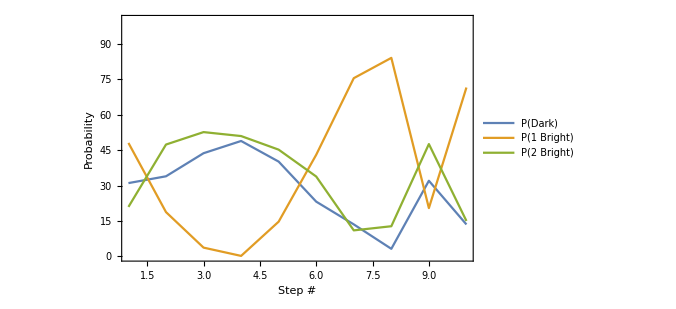

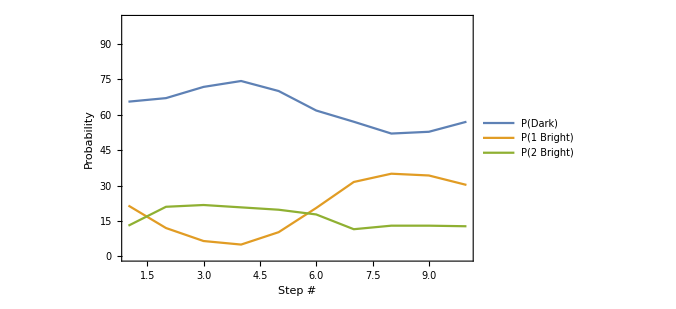

```mathematica
ListLinePlot[Transpose[probabilities], Frame-> True, ImageSize-> 500, PlotRange->{All,{0, 100}},  FrameLabel-> {"Step #", "Probability"}, FrameStyle->{Bold, Black}, LabelStyle->16, PlotLegends->{"P(Dark)", "P(1 Bright)", "P(2 Bright)"}]
ListLinePlot[{400 - onebright - twobright,onebright, twobright}/4, Frame-> True, ImageSize-> 500, PlotRange->{All,{0, 100}},  FrameLabel-> {"Step #", "Probability"}, FrameStyle->{Bold, Black}, LabelStyle->16, PlotLegends->{"P(Dark)", "P(1 Bright)", "P(2 Bright)"}]
```

## Parity Curve Measurement

{48.0344,18.7475,3.70901,0.202489,14.6977,43.0215,75.4445,84.0379,20.4439,71.4935}

{20.9403,47.3462,52.6142,50.9417,45.1798,33.8075,11.0101,12.7618,47.548,14.9941}

{48.0344,18.7475,3.70901,0.202489,14.6977,43.0215,75.4445,84.0379,85.4439,71.4935}

{20.9403,47.3462,52.6142,50.9417,45.1798,33.8075,11.0101,12.7618,10,14.9941}

{31.0253,33.9062,43.6767,48.8559,40.1225,23.171,13.5454,3.20032,4.55614,13.5124}

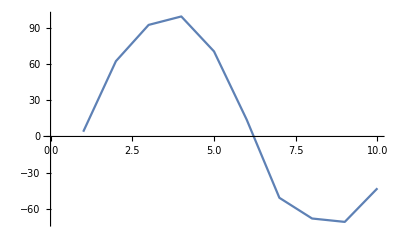

{0.0393125,0.625049,0.92582,0.99595,0.706045,0.139569,-0.50889,-0.680759,-0.708877,-0.42987}

{π/10,π/5,(3 π)/10,(2 π)/5,π/2,(3 π)/5,(7 π)/10,(4 π)/5,(9 π)/10,π}

{A0→0.110335,A→-0.897094,ϕ0→0.912997}

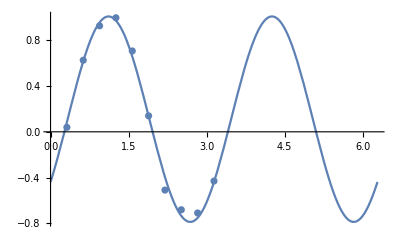

```mathematica
probone = Transpose[probabilities]⟦2⟧
probtwo = Transpose[probabilities]⟦3⟧
probone = {48.03437337801208,18.74752963041468,3.7090083019988063,0.20248913472935273,14.697747925721059,43.021532611248304,75.44448835865613,84.03792967585034,85.44386238389442,71.49348083904447}
probtwo = {20.940339493429555,47.34624107822742,52.6142499624722,50.941656789147906,45.1797708415646,33.807454439971266,11.010140921182643,12.761754247871679,10,14.99407348718059}
probzero = 100 - probone-probtwo

ListLinePlot[probzero + probtwo - probone]

parityYdat = (probzero + probtwo - probone)/100
parityXdat = Table[π/10*i, {i, 1, 10}]
fitParams = FindFit[Transpose[{parityXdat, parityYdat}], A0 + A Cos[2 ϕ + ϕ0],  {{A0, 0}, {A,1}, {ϕ0, 0}}, ϕ]
Show[Plot[A0 + A Cos[2 ϕ + ϕ0]/.fitParams , {ϕ, 0, 2π}],
	 ListPlot[Transpose[{parityXdat, parityYdat}]]]
```

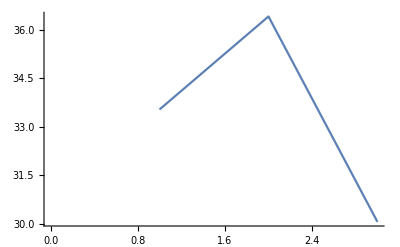

```mathematica
ListLinePlot[probabilities⟦1⟧ + probabilities⟦3⟧ - probabilities⟦2⟧]
```